# Mandelbrot

Progetto d’esame  2021-2022
Traccia n° 2
componenti del gruppo : Nicole Mietto e Lorena Escribano Huesca

## Introduzione

Cominciamo dall’inizio, cosa è l’insieme di Mandelbrot?
L’insieme di Mandelbrot è 
Ovvero, l’insieme dei punti del piano complesso tale che    non va all’.
La sucessione può essere definita come l’applicazione recursiva del polinomio , cominciando in   (il suo unico punto critico).

Se ci concentriamo ora nel polinomio , vediamo che in realtà dipende da due parametri,  e ,  anche se in modo diverso. Fissando un , chiamiamo il piano in cui si muove ,  il piano dinamico; e fissando  , otteniamo il piano parametrico, in cui   giace.
Pertanto, per ogni  , il piano dinamico di  può essere decomposto in due modi:
◼ Tenendo conto della divergenza delle orbite, possiamo dividerlo tra l’insieme dei punti la cui orbita è limitata,   (questo insieme è chiamato anche insieme di Julia pieno), e l’insieme dei punti la cui orbita non è limitata, 
◼ In termini di stabilità della dinamica, possiamo dividerla nell’insieme di Julia, , in cui la dinamica è caotica, e nell’insieme stabile, in cui non lo è.
Tenendo conto di questa divisione, si verifica che  , poiché piccoli spostamenti in quest’area faranno sì che un punto con un’orbita vincolata diventi un’orbita non vincolata, e viceversa.

A lezione si sono già trattati alcuni aspetti dell’insieme di Mandelbrot, in questo progetto vogliamo approfondire nuove caratteristiche di questo insieme ricchissimo di particolari proprietà.

## Le componenti iperboliche e la loro relazione con le orbite periodiche attrattive

Illustriamo alcuni importanti risultati

Teorema di A. Douady, J. H. Hubbard e D. Sullivan
Per ogni componente iperbolica W dell’insieme di Mandelbrot la derivata di P^n(z_0) ( denominata ρ_W ) ( cioè dell’iterata n-esima di z^2+c  calcolata  su un elemento del ciclo di periodo n ) induce un isomorfismo di conformazione 
ρ_W : W → D    ( con D disco aperto di raggio 1 )
che si estende ad un omeomorfismo di W̄ in  D̄ .


Infatti ricordiamo che per essere attrattivo un ciclo di periodo n deve avere modulo della derivata dell’iterata n-esima calcolata in un punto del ciclo < 1. Fatto usato anche a lezione per individuare analiticamente le componenti iperboliche.

Il teorema implica che ogni componente iperbolica ha un unico valore c per il quale il ciclo è superattrattivo cioè ρ_W(c) = 0 , ossia quando 0 è un elemento del ciclo periodico.
Ad esempio nella cardioide, luogo dei cicli periodici attrattivi di periodo 1, si ha c=0 e nel disco di periodo 2 abbiamo c= -1   ( -1→0→-1→...).
Questo significa che il numero di componenti iperboliche di un dato periodo n equivale al numero di valori di c per i quali vi è un ciclo superattrattivo di periodo n.

Vogliamo costruire una funzione che ci restituisca il numero di tali componenti.

si dovrà quindi determinare il numero di radici di :
(ciclo 1) c=0
(ciclo 2) c^2 + c=0
(ciclo 3) (c^2 + (c))^2+c=0
(ciclo 4) ((c^2+c)^2+c)^2+c=0
(ciclo 5) (((c^2+c)^2+c)^2+c)^2+c=0
....
Il problema viene notevolmente semplificato grazie al risultato di A. Gleason : tutte le radici di questi polinomi sono semplici.

Per determinare il numero di cicli di periodo n bisogna togliere dal numero totale di radici ( che sarà il grado del polinomio dato che le radici sono semplici ) tutti i cicli di periodo k che divide n.
Ad esempio dai cicli di periodo 4 bisogna togliere quelli di periodo 2 .
Semplifichiamo la ricerca di tale numero imponendo che, nel caso in cui il ciclo sia di periodo un numero primo i cicli sono 2^(n-1)-1 ,ossia il grado del polinomio dopo n iterazioni -1 (si sono tolti i cicli di periodo 1).

```mathematica
ip[1]:=1
ip[n_]:=Module[{k=2,i=2^(n-1)-1,p=PrimeQ[n]},If[p==False,While[k<=n/2,If[Mod[n,k]==0,i=i-ip[k],None];k++],None];i]
```

```mathematica
ip[100]
```

Un altro importante risultato riguarda i punti di “biforcazione” , ossia i punti di contatto tra una componente iperbolica e un’altra :
se si considera la parametrizzazione della cardioide principale dell’insieme di Mandelbrot ( card[t_]:= (Cos[2 Pi t]+I Sin[2 Pi t])/2 - ((Cos[2 Pi t]+I Sin[2 Pi t])/2)^2 ) si nota che card[p/q] con p e q coprimi ⇒ in corrispondenza di tale punto si dirama dalla cardioide una componente iperbolica di periodo q.

Verifichiamolo

Innanzitutto scriviamo la parametrizzazione della cardioide

```mathematica
card[t_]:= (Cos[2 Pi t]+I Sin[2 Pi t])/2 - ((Cos[2 Pi t]+I Sin[2 Pi t])/2)^2
```

Per prima cosa diamo una lista di punti {1/2, 1/3, 1/4, 1/5, 1/6, 1/7} e mostriamo i corrispondenti punti di biforcazione, dando un’etichetta che indica il periodo delle orbite attrattive corrispondenti.

```mathematica
j= Compile[{ {z,_Complex},{nit,_Integer},{c,_Complex}},  Module[{k=0,w=z,  r=.5+√(.25+Abs[c])},  While[Abs[w]<r  &&   k<nit, w = w^2 + c ; k++];  
                                       0.7 (k+1)/(1+nit) ]  ] ;jgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,c_]:=   ParallelTable[ j[x+I y,nit,c] , {y,ymin,ymax,(ymax-ymin)/ndiv}, {x,xmin,xmax,(xmax-xmin)/ndiv}];
jset[{xmin_,xmax_,ymin_,ymax_},ndiv_,numit_,c_]:=      Graphics@ Raster[      jgrid [{xmin,xmax,ymin,ymax},ndiv,numit,c] ,     {{xmin,ymin},{xmax,ymax}},ColorFunction->Hue  ];
jset[limiti_,ndiv_,numit_,c_,ImSize_]:= Show[ jset[limiti,ndiv,numit,c],Frame->True,   ImageSize->{ ImSize } ] ;
finestra[gr_,{x1_,x2_,y1_,y2_}]:= Show[   gr,   Graphics@Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]   ];
```

```mathematica
mgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_]:=  ParallelTable[j[0,nit, cx+I cy],   {cy,ymin,ymax,(ymax-ymin)/ndiv},  {cx,xmin,xmax,(xmax-xmin)/ndiv}  ];
mset[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,imsize_]:=
Show[      Graphics@Raster [   mgrid[{xmin,xmax,ymin,ymax},ndiv,nit], {{xmin,ymin},{xmax,ymax}}, ColorFunction->Hue ],
                Frame->True,ImageSize->{imsize}];
```

```mathematica
mand=Show[mset[{-1.,0.5,-1.,1.},500,700,500],Graphics[Flatten[Map[{PointSize[0.015],Point[{Re[card[#]],Im[card[#]]}]}&,{1/2,1/3,1/4,1/5,1/6,1/7}]]],Graphics[Style[Table[Text[ToString[n],{Re[card[1/n]]-0.03,Im[card[1/n]]+0.01}],{n,2,7}],Black, Bold,Small,Background->White]]]
```

Come ci si aspettava i punti trovati sono tutti punti di biforcazione. Verifichiamo ora che le orbite periodiche attrattive siano del periodo indicato.
Per le orbite di periodo 2 e 3 ci è già noto, mostriamolo quindi per 4,5,6,7.

```mathematica
orb[c_,z_,nit_]:=Map[  {Re[#],Im[#]}& ,   NestList[ #^2+c &,z,nit]  ]
orb[c_,z_,nit_,ncoda_]:= Take[orb[c,z,nit],-ncoda]
gorb[c_,z_,n_,ncoda_]:=ListPlot[orb[c,z,n,ncoda],PlotRange->2{{-1,1},{-1,1}},PlotStyle->{White,PointSize[0.007]}]
```

Costruiamo una funzione che, dato un valore di c all’interno di una componente iperbolica, restituisce il suo periodo se ≤ del periodo massimo altrimenti restituisce pmax+1 e l’insieme di punti rappresentante l’ultima iterazione del ciclo.
Per fare ciò dobbiamo inserire un indice di tolleranza in modo che possiamo considerare attrattiva l’orbita se il ciclo si avvicina più di tale indice nelle ultime iterazioni dell’orbita ( abbiamo scelto un’orbita di 500 iterazioni ).
Valutiamo solo l’orbita con punto iniziale 0 perchè per il teorema di Fatou ogni ciclo attrattivo per un polinomio attrae almeno un punto critico ( cioè un punto in cui la derivata è 0 ). Nel nostro caso z^2+c  possiede un solo punto critico 0 e vi potrà essere un unico ciclo attrattivo per il valore di c corrispondente.

```mathematica
period1[cc_,pmax_,toll_]:=Module[{periodo= 1,orbita=orb[cc,0,500]},While[periodo<=pmax && Count[Map[Abs[#[[1]]+I#[[2]]]<toll &,Table[orbita[[501-t*periodo]]-orbita[[501-(t+1)*periodo]],{t,0,10}]],False]>=1,periodo=1+periodo];{periodo,Take[orbita,-periodo]}]
```

Definiamo descr che in base al periodo dell’orbita restituisce una stringa descrittiva con il valore di c e il periodo dell’orbita.

```mathematica
descr[c_,pmax_,p_]:=If[p<=pmax,"c="<>ToString[c]<>", orbita attrattiva di periodo "<>ToString[p],"c="<>ToString[c]<>", orbita non di periodo≤"<>ToString[pmax]]
```

Definiamo graf che mi riporta l’ultima iterazione del ciclo con la descrizione delle proprietà dell’orbita.

```mathematica
graf[pmax_,toll_,c_]:=Module[{p=period1[c,pmax,toll]},Show[jset[{-2,2,-2,2},400,150,c],ListPlot[p[[2]],PlotStyle->{White,PointSize[0.01]}],PlotRange->{{-2,2},{-2,2}},Frame->True,ImageSize->400,PlotLabel->descr[c,pmax,p[[1]]]] ]
```

Mostriamo degli esempi con alcuni valori di c all’interno delle componenti iperboliche individuate sopra e verifichiamo che abbiano il periodo indicato.

```mathematica
p14=graf[20,0.001,0.2761+0.541 I];
p15=graf[20,0.001,0.372+0.3361 I];
p16=graf[20,0.001,0.3905+0.217 I];
p17=graf[20,0.001,0.37536+0.1451 I];
```

```mathematica
Grid[{{p14,p15},{p16,p17}}]
```

Osservazioni

Anche nella componente iperbolica di periodo 2 sembra funzionare similmente ma le orbite in corrispondenza della componente iperbolica relativa al punto di biforcazione saranno di periodo 2*q.

Scriviamo innanzitutto la parametrizzazione della componente iperbolica di periodo 2, in modo tale che in corrispondenza di t=0 si ha il punto di biforcazione con la cardioide.

```mathematica
ip2[t_]:= {0.25*Cos[t* 2 Pi]-1,0.25*Sin[t* 2 Pi]}
```

Mostriamo i punti di biforcazione che intendiamo analizzare e scegliamo per ognuno di essi un punto all’interno della componente iperbolica.

```mathematica
mand=Show[mset[{-1.5,-0.5,-.4,.4},500,700,500],Graphics[Flatten[Map[{PointSize[0.015],Point[ip2[#]]}&,{1/2,1/3,1/4,1/5,1/6,1/7}]]],Graphics[Style[Table[Text[ToString[n],ip2[2/n]+{-0.03,-0.02}],{n,4,14,2}],Black, Bold,Small,Background->White]]]
```

Come prima mostriamo degli esempi per dei c all’interno delle componenti iperboliche.

```mathematica
p24=graf[20,0.001,-1.3275+0.007 I];
p26=graf[20,0.001,-1.1401+0.2426 I];
p28=graf[20,0.001,-1.+0.261 I];
p210=graf[20,0.001,-0.9193+0.2478 I];
p212=graf[20,0.001,-0.8708+0.2221 I];
p214=graf[20,0.001,-0.84088+0.19945 I];
```

```mathematica
Grid[{{p24,p26},{p28,p210},{p212,p214}}]
```

## Il potenziale

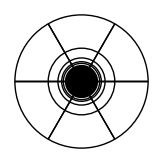
A lezione abbiamo osservato come creare l’immagine grafica dell’insieme di Mandelbrot:  valutando la dinamica di z^2+c per  z_0= 0 .
Si è creata un’ immagine a colori che mostrava, in base alla velocità di fuga ( n° di iterazioni necessarie prima di uscire dal disco di raggio 2, in cui sappiamo essere contenuto l’insieme di Mandelbrot ),  lo spazio dei parametri c. Quindi il significato delle sfumature che si osservavano nell’output finale riguardava la velocità di fuga all’∞  di 0. 

                -Graphics-     per vedere meglio la velocità di fuga all’infinito ( con maggiori sfumature ) si diminuiscono le iterazioni di controllo dei punti dell’insieme.

il potenziale su J_0
Il concetto di potenziale si può introdurre in maniera intuitiva pensando all’insieme di Julia relativo a c= 0 (un disco di raggio 1 centrato nell’origine ). Si nota che la formula che delinea il potenziale ricorda quella che descrive il potenziale generato da un filo infinito di cariche (fig. 1).  

-Graphics-                               -Graphics-
                         fig. 1                                                                                fig. 2
                         
In questo caso si definisce potenziale p(z)= log_2 | z | con dominio fuori dal disco di raggio 1. Notiamo che, come nel caso del filo carico, le superfici equipotenziali sono concentriche all’origine. Inoltre  si definiscono linee di campo le semirette uscenti dall’origine che rappresentano la rotazione nel piano che esegue z_0 nelle sue iterazioni ( la dinamica di z^2 se rappresentato con le coordinate polari, raddoppia ad ogni titerazione il proprio argomento ϕ ). Le superfici equipotenziali e le linee di campo sono illustrate nella figura 2.

Insiemi di Julia
In generale vale il Riemann mapping theorem che permette di relazionare con una corrispondenza biunivoca il potenziale di J_0 con quello di un qualsiasi insieme di Julia connesso.
Si sa che in generale le linee equipotenziali non saranno delle circonferenze, se non quando consideriamo il potenziale distante dall’iniseme di Julia; questo perchè per   z_0 con un modulo relativamente più grande la dinamica di  z^2+c  si approssima a quella di  J_0 poichè c è trascurabile rispetto al termine quadratico. 

Si definiscono ( con k≥0 ):
 Q_c^(k)= { z_k|  |z_0 | ≤ r(c) }  ( immagini dopo k iterazioni di Q_c^(0) ) 
 Q_c^(-k)= { z_0 |  |z_k | ≤ r(c) }  ( preimmagini dopo k iterazioni di Q_c^(0) )
 D^(k) = { z | log_2 | z | ≤ 2^k }  ( = { z |   |z | ≤ 2^(2^k) } )
 con r(c) raggio del disco in cui è contenuto l’insieme di Julia ( max { |c|, 2 } ).
 I D^(k) nel caso di J_0 sono insiemi la cui frontiera è rappresentanta da una linea di campo equipotenziale: p_0(z)=log_2 | z | = 2^k .
 Notiamo che  J_c = k→^lim∞   Q_c^(-k) = k→^lim∞ { z_0 |  |z_k | ≤ max { |c|, 2 }  }  cioè l’insieme dei valori iniziali per cui l’orbita del punto rimane circoscritta.
 Si vedono inoltre queste inclusioni: Q_c^(-k)⊃ Q_c^(-k-1) e  Q_c^(k+1)⊃ Q_c^(k) ( con k ≥ 0 ) poichè si dimostra facilmente che se |z| > r(c) ⇒ |z^2 + c | > |z| ; perciò nel primo caso si ha Q_c^(-k)⊃ Q_c^(-k-1) poichè supponendo z_0 ϵ Q_c^(-k-1) se per assurdo z_0^2 + c iterata k volte > r(c) ⇒ |z_(k+1) | > | z_k| > r(c) che è un assurdo per l’ipotesi z_0 ϵ Q_c^(-k-1), mentre il secondo caso è ovvio ( se z_0 ϵ Q_c^(k) allora se prendo una sua preimmagine in Q_c^(-1) allora la sua immagine iterata k+1-esima è z_k, la stessa dell’orbita di z_0 all’iterarata k-esima).

Nel caso di J_0 otteniamo che Q_0^(k-l) ( D^(l) ) = Q_0^(k) ( D^(0) )  ∀ l .
Infatti notiamo che: 
 Q_0^(k)= { z_k|  |z_0 | ≤ 2 } = {( (z_(k-1)))^2 |  |z_0 | ≤ 2 } = {( (z_0))^(2^k) |  |z_0 | ≤ 2 } = D^(k) e
 Q_0^(-k)= { z_0 |  |z_k | ≤ 2 } = { z_0 |  |z_(k-1) |^2 ≤ 2 } = { z_0 |  |z_0 |^(2^k) ≤ 2 } ={ z_0 |  |z_0 | ≤ 2^(1/2^k) } = { z_0 |  |z_0 | ≤ 2^(2^-k) } = D^(-k)
 e quindi Q_0^(k-l) ( D^(l) ) = Q_0^(k-l) ( Q_0^(l) )  = Q_0^(k-l) ( Q_0^(l) ( Q_0^(0) ) ) = Q_0^(k-l+l) = Q_0^(k) ( D^(0) )  poichè sono preimmagini o immagini iterate di z_0 .

Nei casi in cui c≠ 0 l’uguaglianza non vale ma è vero che P_c^(k)= l→^lim∞   Q_c^(k-l) ( D^(l) ) converge ad un insieme la cui frontiera è un insieme equipotenziale.
Poichè  in  l→^lim∞  D^(l) gli elementi con |z| relativamente grande approssimano la propria dinamica a quella di z^2 ⇒ gli elementi sulla frontiera vengono mandati su una linea equipotenziale analoga a quella per J_0 mentre gli altri saranno circoscritti dalla linea appena descritta, si avrà quindi  l→^lim∞  D^(l) =   Q_c^(l)  ⇒ P_c^(k)= l→^lim∞   Q_c^(k-l) ( D^(l) ) =   Q_c^(k-l+l) =   Q_c^(k).
L’insieme P_c^(k) si può anche riscrivere in questo modo : P_c^(k) = { z_0 |   l→^lim∞ (log_2 |z_l|)/2^l ≤ 2^k } , 
infatti    P_c^(k)= l→^lim∞   Q_c^(k-l) ( D^(l) ) = l→^lim∞  { z_0 |  |z_(l-k) | ≤  2^(2^l) } = l→^lim∞ { z_0 |   log_2 | z_(l-k) | ≤ 2^l } = l→^lim∞ {  z_0 | (log_2 |z_(l-k) |)/2^(l-k) ≤ 2^k } = l→^lim∞ { z_0 |  (log_2 |z_l |)/2^l ≤ 2^k } .
La funzione potenziale è quindi in generale :   p_c^(k)= { z_0 |   l→^lim∞ (log_2 |z_l|)/2^l } .

Il potenziale sull’insieme di Mandelbrot
Il concetto di potenziale si generalizza anche all’insieme di Mandelbrot. Qui, a differenza degli insiemi di Julia, ci si sta muovendo sul piano dei parametri c quindi non si vede una vera e propria dinamica come nel caso degli insiemi di Julia.
La funzione potenziale si definisce in modo più o meno analogo per gli insiemi di Julia.
Definito  R^(-k)(T) = { c ϵ ℂ | z_k ϵ T ,  z_0= c } , si identifica, come nel caso di Q_c^(k) ,  M_k = l→^lim∞   R^(k-l) ( D^(l) )   ( D^(l) sempre definito nel modo precedente ); questo insieme si può anche riscrivere in modo analogo a quanto visto per gli insiemi di Julia come M_k = { c ϵ ℂ |  l→^lim∞ (log_2 |z_l|)/2^l ≤ 2^k , z_0= c } .
E quindi la funzione potenziale è definita :   p_M(c) =    l→^lim∞ (log_2 |z_l|)/2^l  ,    z_0= c .

Il potenziale è uno strumento che permette anche di approssimare l’insieme di Mandelbrot M= k→^lim∞   M_-k ( come infatti accade anche per gli insiemi di Julia ) .
Nel seguito vogliamo illustrare la decomposizione binaria dell’insieme di Mandelbrot, ossia una decomposizione dello spazio dei parametri c in modo tale che siano visibili sia le linee equipotenziali sia le linee di campo dell’insieme, entrambe in corrispondenza biunivoca con l’analoga costruzione su J_0.

Richiamiamo le funzioni già viste a lezione per costruire l’insieme di Mandelbrot :

```mathematica
j= Compile[{ {z,_Complex},{nit,_Integer},{c,_Complex}},  Module[{k=0,w=z,  r=.5+√(.25+Abs[c])},  While[Abs[w]<r  &&   k<nit, w = w^2 + c ; k++];  
                                       0.7 (k+1)/(1+nit) ]  ] ;jgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,c_]:=   ParallelTable[ j[x+I y,nit,c] , {y,ymin,ymax,(ymax-ymin)/ndiv}, {x,xmin,xmax,(xmax-xmin)/ndiv}];
jset[{xmin_,xmax_,ymin_,ymax_},ndiv_,numit_,c_]:=      Graphics@ Raster[      jgrid [{xmin,xmax,ymin,ymax},ndiv,numit,c] ,     {{xmin,ymin},{xmax,ymax}},ColorFunction->Hue  ];
jset[limiti_,ndiv_,numit_,c_,ImSize_]:= Show[ jset[limiti,ndiv,numit,c],Frame->True,   ImageSize->{ ImSize } ] ;
finestra[gr_,{x1_,x2_,y1_,y2_}]:= Show[   gr,   Graphics@Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]   ];
```

```mathematica
mgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_]:=  ParallelTable[j[0,nit, cx+I cy],   {cy,ymin,ymax,(ymax-ymin)/ndiv},  {cx,xmin,xmax,(xmax-xmin)/ndiv}  ];
mset[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,imsize_]:=
Show[      Graphics@Raster [   mgrid[{xmin,xmax,ymin,ymax},ndiv,nit], {{xmin,ymin},{xmax,ymax}}, ColorFunction->Hue ],
                Frame->True,ImageSize->{imsize}];
```

decomposizione binaria dell’insieme di Mandelbrot

Si definisce L^k = { c ϵ ℂ | 2^(k-1) < p_M(c) ≤ 2^k} = M_k \ M_(k-1)  ( differenza insiemistica ) .
Nonostante non vi sia la medesima interpretazione dinamica che invece vi era con gli insiemi di livello per gli insiemi di Julia, dove gli L^k definiti in modo analogo venivano trasformati nell’insieme di livello successivo, possiamo comunque definire una decomposizione ( la decomposizione per gli insiemi di Julia utilizza le preimmagini della decomposizione precedente in L^(k+1), quindi ad ogni iterazione la suddivisione dell’insieme di livello successivo raddoppia ).

La suddivisione di L^k in 2^ncelle denominate con b_1 b_2..... b_n si esegue in questo modo :
- per ogni c ϵ L^k si calcola la n-esima iterata di z^2+c  con z_0= c . Si dividono le celle valutando se la parte immaginaria Im[z_n]≥0 ( avranno la forma b_1..... b_(n-1)0 ) o meno ( b_1..... b_(n-1)1 ) .
- la denominazione binaria delle celle avviene in maniera antioraria, quindi 2 celle vicine hanno in corrispondenza della n-esima iterata una parte immaginaria  ≥0 e l’altra <0 .

Per prima cosa decomponiamo lo spazio tramite gli L^k .
Invece di valutare all’infinito il limite di p_M(c), si può invece sfruttare la proprietà che gli M_k per indici superiori a 3 sono quasi identici ai D^(k) ( dischi di raggio 2^(2^k) ), questo sempre per l’approssimazione della dinamica di z^2+c a quella di z^2. Per gli altri M_k utilizziamo il fatto che se iteriamo nuovamente l’insieme M_k otteniamo M_(k+1) .

Definiamo quindi la funzione compilata pot che restituisce l’indice di M_k più piccolo ma ≥ 4 - valore massimo ( un parametro della funzione ) nel quale è contenuto c .
La funzione valuta dopo quante iterate c esce da M_3 ossia da un disco di raggio 2^(2^3) e restituisce 4 - n° di iterate .

```mathematica
pot=Compile[{{ pmax,_Integer},{c,_Complex}},Module[{k=0,w=c},While[   k<pmax &&Abs[w]<=256,k+=1;  w = w^2 + c];  4-k]];
```

potgrid assegna un valore a ciascun punto sulla griglia in cui è stata divisa la “finestra” presente tra i parametri della funzione : 1 se il punto è nell’insieme di Mandelbrot, 0.9 se il punto è contenuto in un insieme del tipo M_(2k) e 0.1 altrimenti.

```mathematica
potgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,pmax_]:= ParallelTable[If[j[0,500,cx+I cy]==0.7,1,Mod[pot[pmax,cx+I cy],2]*0.8+0.1],   {cy,ymin,ymax,(ymax-ymin)/ndiv},  {cx,xmin,xmax,(xmax-xmin)/ndiv}  ]
```

potset utilizza la funzione Raster di Graphics per colorare la tabella dei valori creata con potgrid

```mathematica
potset[{xmin_,xmax_,ymin_,ymax_},ndiv_,pmax_,imsize_]:=
Show[      Graphics@Raster [   potgrid[{xmin,xmax,ymin,ymax},ndiv,pmax], {{xmin,ymin},{xmax,ymax}},ColorFunction->Hue],
                Frame->True,ImageSize->{imsize}]
```

Vediamo un esempio

```mathematica
potset[{-2.,1,-1.5,1.5},500,12,500]
```

Ora vogliamo dividere ogni L^k con la decomposizione vista sopra.

Definiamo una funzione compilata bin che dato un valore c restituisce  1 se Im[z_n]≥0 ( con n n° di iterazioni ) altrimenti 0 .

```mathematica
bin=Compile[{ {nit,_Integer},{c,_Complex}},Module[{k=1,w=c},While[   k<=nit,k++; w = w^2 + c];Boole[Im[w]>=0]]];
```

binarygrid valuta ogni elemento della griglia e assegna :
- 1 se c è contenuto nell’insieme di Mandelbrot;
- 0.4 se c è contenuto in L^k con k< L^(3-pmax) cioè il più piccolo L^k in cui è stato suddiviso lo spazio;
- 0.1 se partendo la suddivisione binaria da L^2 (che non è contenuto nell’area di piano mostrata nel disegno ) in L^l ho che Im[z_(3-l)]<0;
- 0.9 altrimenti 

binaryset ha la funzione di colorare l’area di piano mostrata nel disegno

```mathematica
binarygrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,pmax_]:= ParallelTable[Module[{p=pot[pmax,cx+I cy]},If[j[0,500,cx+I cy]==0.7,1.,If[p==4-pmax,0.4,bin[3-p,cx+I cy]*0.8+0.1]]],   {cy,ymin,ymax,(ymax-ymin)/ndiv},  {cx,xmin,xmax,(xmax-xmin)/ndiv}  ]
```

```mathematica
binaryset[{xmin_,xmax_,ymin_,ymax_},ndiv_,pmax_,imsize_]:=
Show[      Graphics@Raster [   binarygrid[{xmin,xmax,ymin,ymax},ndiv,pmax], {{xmin,ymin},{xmax,ymax}}],
                Frame->True,ImageSize->{imsize}]
```

```mathematica
binaryset[{-2.,1,-1.5,1.5},700,15,700]
```

Nel disegno finale si notano sia la suddivisione con gli insiemi di livello L^k sia le linee di campo .

## La relazione fra insieme di Mandelbrot e insiemi di Julia. I “punti di Misiurewicz” e i “dendriti”.

Vediamo ora la relazione tra gli insiemi di Mandelbrot e di Julia, per i quali è di grande interesse introdurre i punti di Misiurewicz.
Un parametro  è un punto di Misiurewicz se la orbita di z_0= 0 in  è strettamente preperiodica. Cioè, l’orbita entra in un ciclo che non include lo zero. I due esempi più semplici sono  c=i e c= -2:

```mathematica
P[z_,c_]:=z^2+c;
successione[z_,nit_,c_]:=NestWhileList[P[#,c]&,z,Abs[#]<=2 &, 1, nit];
successione[0,5,I]
```

{0,ⅈ,-1+ⅈ,-ⅈ,-1+ⅈ,-ⅈ}

```mathematica
successione[0,5,-2]
```

{0,-2,2,2,2,2}

L’ orbita di 0 con parametro c=i è strettamente periodica di periodo k=2, perché   z_(2+2)= z_4= z_2
Mentre che l’ orbita di 0 in c=-2 è di periodo k=1, perché  z_(2+1)= z_3= z_2

Si può provare che se  è un punto di Misiurewicz, allora   J_c=K_c ( ossia l’insieme di Julia coincide con la propria chiusura ) e, dato che l’orbita rispetto a   è limitata/vincolata (per essere ciclica in certo punto), si ha che .
Quando un insieme di Julia verifica la propietà PM, questo si denomina dendrita.
Per disegnare gli insiemi di Julia, utilizziamo le funzioni viste a lezione:

```mathematica
j= Compile[{ {z,_Complex},{nit,_Integer},{c,_Complex}},   
			Module[{k=0,w=z,  r=.5+√(.25+Abs[c])},  While[Abs[w]<r  &&   k<nit, w = w^2 + c ; k++];    
			0.7 (k+1)/(1+nit) ]   ] ;
jgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,c_]:=   ParallelTable[ j[x+I y,nit,c] , {y,ymin,ymax,(ymax-ymin)/ndiv}, {x,xmin,xmax,(xmax-xmin)/ndiv}];
jset[{xmin_,xmax_,ymin_,ymax_},ndiv_,numit_,c_]:=      Graphics@ Raster[      jgrid [{xmin,xmax,ymin,ymax},ndiv,numit,c] ,     {{xmin,ymin},{xmax,ymax}},ColorFunction->Hue  ];
jset[limiti_,ndiv_,numit_,c_,ImSize_]:= Show[ jset[limiti,ndiv,numit,c],Frame->True,   ImageSize->{ ImSize } ] ;
finestra[gr_,{x1_,x2_,y1_,y2_}]:= Show[   gr,   Graphics@Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]   ]
```

```mathematica
jset[{-1,1,-1,1},500,15,I]
```

-Graphics-

Qui possiamo vedere l’insieme di Julia per c= i e sotto lo facciamo per c=-0.101096 + 0.956287 i :

```mathematica
jset[{-1,1,-1,1},1000,100,-.101096+.956287 I]
```

-Graphics-

Risulta che i centri  e i punti di Misiurewicz formano l’insieme dei valori di  c per il quale l’orbita di 0 per   è finita ( cioè poi ripete sempre se stessa o parte di essa ).
I centri si trovano all’interno dell’insieme di Mandelbrot ( abbiamo visto anche che ne è presente soltanto uno per componente iperbolica )  mentre che i punti di Misiurewicz si trovano nella frontiera.
In più, si può dimostrare che se   si trova in una componente iperbolica oppure se è un punto di Misiurewicz, allora l’ insieme di Julia è localmente conesso: cioè per ogni z∈k_c e per ogni intorno  di , esiste un intorno connesso   in di .
Se  è localmente conesso, allora il terorema di Carathéodory assicura che l’applicazione  
si estende di forma continua alla frontiera:
  definita per .
Quindi se  è localmente conesso, allora qualsiasi raggio esterno   termina in un punto (ϑ) 
 dell’insieme di Julia e  è una parametrizzazione di .  Un punto dell’insieme di Julia deve essere il punto di arrivo di diversi raggi.
Per vedere questo effetto correttamente, lo disegnamo:

Inanzitutto disegniamo l’insieme di Julia per c=ⅈ.
Dopo, con la funzione jb  creamo una lista di coordenate {x,y,z}, essendo z la coordenata di Bottcher del numero complesso x+yⅈ, dove x recorrono l’intervallo [-2, 2] ogni uno.
La funzione theRays ritorna una lista con 10 valori presi tra -π  e  π 
La funzione rayTable è il cuore del algoritmo per potere disegnare i raggi:
Facciamo una lista 
Scegliamo tutti gli elementi della lista jb tale che il modulo della coordenata di Bottcher di un numero complesso x+yⅈ, cioè la 3 coordinata degli elementi in jb, è compresso tra θ - 0.001 e θ + 0.001, essendo la coordinata θ un numero della lista theRays.
Finalmente disegniamo la linea del raggio:  consiste nelle coordinate x e y della lista jb (corrispondono ai primi e secondi  argumenti delle coordenate  {x,y,z} della lista jb) tale che la coordenata di Bottcher di un numero complesso x+yⅈ verifiche la condizione implementata nel modulo Select.

```mathematica
theC =I;
jsp = jset[{-2,2,-2,2},400,100,theC]

jb = Flatten[Table[{x, y, JuliaSetBoettcher[theC, x + I y, MaxIterations -> 30]}, {y, -2, 2, .01}, {x, -2, 2, .01}], 1];
theRays = Array[# &, 10, {-Pi, Pi}];
rayTable = Table[theRayPoints = Select[jb, (theta - 0.001) < Arg[#[[3]]] < (theta + 0.001) &];
				Graphics@Line@({#[[1]], #[[2]]} & /@ theRayPoints),{theta, theRays}];
Show[{jsp, rayTable}]
```

-Graphics-

-Graphics-

Si può notare un raggio strano, così come alcuni raggi che non colpiscono l’insieme. Ciò è dovuto a problemi di accuratezza nella rappresentazione numerica. Per maggiori dettagli su questo argomento, si possono consultare diversi articoli scritti da Douady.

Abbiamo visto che i punti di Misiurewicz sono punti dello spazio dei parametri il cui comportamento dinamico è tale che coincidono .
Infine, per stabilire la relazione dei fatti visti finora con l’insieme di Mandelbrot, utilizziamo il teorema di Montel (pagina 100 del libro), da cui deriva che:
I punti di Misiurewicz sono densi nella frontiera di 
La frontiera di   è contenuta nella chiusura dei centri delle componenti iperboliche.
Siamo particolarmente interessati al punto 1. in quanto mette in relazione diretta i punti che producono insiemi di Julia pieni localmente connessi con i punti di frontiera dell’insieme di Mandelbrot. Inoltre, è stato dimostrato che esiste una somiglianza tra l’insieme di Julia e l’insieme di Mandelbrot intorno a qualsiasi punto di Misiurewicz. 
Consideriamo il punto di Misiurewicz  c=-0.101096+ i 0.956287 .

```mathematica
A = -0.101096;
B = 0.956287;
theC = A + I B;
jset[{A-0.01,A+0.01,B-0.01,B+0.01},1000,100,theC]
```

-Graphics-

Usando le funzioni definite a lezione per disegnare l’insieme di Mandelbrot:

```mathematica
mgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_]:=ParallelTable[ j[0.,nit,cx+I cy] , {cy,ymin,ymax,(ymax-ymin)/ndiv}, {cx,xmin,xmax,(xmax-xmin)/ndiv}];

mset[{xmin_,xmax_,ymin_,ymax_},ndiv_,numit_,ImSize_]:=Graphics[Raster[mgrid [{xmin,xmax,ymin,ymax},ndiv,numit] ,
													{{xmin,ymin},{xmax,ymax}},ColorFunction->Hue], Frame->True, ImageSize->{ ImSize }]
```

```mathematica
mset[{A-0.01,A+0.01,B-0.01,B+0.01},1000,200,400]
```

-Graphics-

In questo grafico si nota chiaramente la somiglianza con l’insieme Julia precedente!

## La universalità dell’insieme di Mandelbrot

L’universalità dell’insieme di Mandelbrot si riferisce al fatto che copie di esso si trovano non solo nel piano parametrico dei polinomi quadratici, ma in molte altre famiglie uniparametriche di funzioni analitiche.
Il motivo è che queste funzioni si comportano localmente come polinomi quadratici.
Una funzione analitica f da U’ in U si chiama polynomial-like of degree d se U’ e U sono isomosfi a un disco in ℂ con 
e f di grado d.
Consideriamo adesso una familia one-parameter Λ, isomorfa a un disco, di polynomial-like mappings di grado 2 :   

con c∈Λ.  C’è un unico punto critico 
Si può provare che Λ contiene una copia dell’insieme di Mandelbrot se esiste un sottoinsieme chuiso A in  Λ  tale che A è isomorfo a  ,  e tale che   appartiene a  per tutti  c in  Λint(A), e tale che   gira attorno a 0 una volta λ descrive la frontiera di A.
Usando questo risultato, capiremo perché si vedono piccole copie del insieme di Mandelbrot dentro se stesso.
Adesso vediamo un esempio di una familia one-parameter di mappe analitiche ottenuta apartire dal metodo de Newton trovando radici di un polinomio cubico.

#### Esempio d’ applicazione del metodo di Newton.

Il metodo di Newton serve per trovare radici di un polinomio. 
Se conosciamo una soluzione aprossimata z_0 della equazione f(z)=0 sufficentemente vicina alla soluzione esatta dell’equazione a, allora possiamo ottenere una megliore aprossimazione  z_1 di a facendo:   z_1= z_0 - f (z_0)/f ’(z_0)
Iterando questo procedimento otteniamo una sequenza di numeri z_n che converge a a. 
Inanzitutto definiamo la funzione iterativa del metodo di Newton che fornisce la serie convergente alla radice a del polinomio z^n-1.

```mathematica
NewtonIteration[f_,z_] := z - (f - 1)/Derivative[1][Function[z,f]][z];
```

Faciamo un esempio applicando il metodo di newton al polinomio di grado generico n , f(z)=z^n-1

```mathematica
FunzioneNewton=Simplify[NewtonIteration[z^n,z]]
```

Ricordiamo come funziona il modulo FixedPointList. È una funzione già implementata da Wolfram Mathematica che fornisce una lista di punti tale che, cominciando nel punto iniziale  0.5-0.5 ⅈ , tra 10 iterazione , vanno aprossimandosi al funto fisso della funzione FunzioneNewton.

```mathematica
FixedPointList[# (n-1+#^(-n))/n &/. n->3, .5-.5I,10]
```

{0.5-0.5 ⅈ,0.333333+0.333333 ⅈ,0.222222-1.27778 ⅈ,-0.0383816-0.784948 ⅈ,-0.562722-0.575953 ⅈ,-0.387094-0.897933 ⅈ,-0.497419-0.852099 ⅈ,-0.499967-0.866227 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ}

La seguente funzione, newt, calcola il punto fisso della funzione FunzioneNewton cominciando nel punto z_0, passato come parametro.
Abbiamo fissato 35 come numero massimo di tentativi per calcolare il punto fisso.

Perché calcoliamo il punto fisso della funzione definita sopra? 
Faccendo  z_1=z_0- f(z_0)/f '(z_0), calcolando un nuovo  z_1, e così via, il processo può essere ripetuto fino a convergere a un punto fisso (che è appunto una radice di f(z)=z^n-1)
La funzione newt retorna il punto fisso trovato tra massimo, 35 iterazioni.

```mathematica
newt = Compile[{{n, _Integer}, {z, _Complex}}, 
      Arg[FixedPoint[# (n-1+#^(-n))/n &, z, 35]]];
```

Adesso facciamo un disegno usando il comando Show (richiede molto tempo per l’esecuzione, per cui ho lasciato l’immagine finale)
Per mezzo dei comandi GraphicsArray e Partition possiamo ottenere un quadro visivamente buono di ciò che stiamo facendo per ciascun n=3, 4, 5 ....11 (grado del polinomio z^n-1). 
La funzione  Partition [list, l] : Particiona una lista in sottoliste di lunghezza l=3. Quindi richiede come parametro una lista. 
Dentro di questo modulo si facciono tre azioni.
1) Con un Table variamo il grado del polinomio f.
2) Una volta fissato n=3,4,....11, con un Table, passiamo attraverso (quasi) tutti i numeri complessi del rettangolo complesso [-1.1, 1-1] x [ 1.1,-1.1] , questi numeri complessi saranno utilizzati come punto di partenza per la funzione newt.
3) La funzione ListDensityPlot[{{f_(1 1),...,f_(1 n)},...,{f_(m 1),...,f_(m n)}}] genera un grafico di densità omogeneo apartire da un array di valori, di questa forma tutti i numeri complessi z_0 del rectangulo complejo [-1.1, 1-1] x [ 1.1,-1.1] tali che attraverso della funzione newt converge al punto fisso a , tendran el mismo tono en la representacion.

Quindi per esempio per n=3, ci sono tre soluzioni del polinomio f(z)=z^n-1 , in consequenza tre punti fissi della funzione FunzioneNewton e per tanto tre colori diversi forniti dal modulo ListDensityPlot.

Alla fine facciamo un Timing per calcolare il tempo di esecuzione.

```mathematica
Show[GraphicsArray[Partition[Table[ListDensityPlot[Table[newt[n,b+a I],{a,-1.1,1.1,0.005},{b,1.1,-1.1,-0.005}],
Mesh->False,
DisplayFunction->Identity,
PlotRange->All,
ColorFunction->Hue,
Frame->False],{n,3,11}],3],GraphicsSpacing->0.05]]//Timing
```

{107.625,-Graphics-}

Adesso ho provato a disegnare l’insieme di Julia associato alla funzione N_c(z)= z - (f_c(z))/(f'_c(z)) essendo f_c(z )= (z-1)(z+ 1/2-c)(z+1/2+c) il polinomio cubico di radici z_0=1 ,  z_1= -1/2-c  , z_2=-1/2+c , ma non ho riuscito a calcolare il raggio di convergenza per la funzione di grado 3, N_c(z), e quindi non ho potuto calcolare l’insieme di Julia associato alla funzione  N_c(z).
Ho provato a disegnarla usando il raggio di convergenza usato per il polinomio

```mathematica
r1 = 1;
r2 = 1/2-c;
r3 = 1/2+c;
P[c_,z_] = (z-r1)(z+r2)(z+r3);
derivataP[c_,z_] = D[P[c,z],z];
NewtonIteration[c_,z_] = z - N(P[c,z])/N(derivataP[c,z]);
			 
Uj= Compile[{ {z,_Complex},{nit,_Integer},{c,_Complex}},  
			Module[{k=0, w=z,  r=.5+√(.25+Abs[c])}, 
					While[Abs[w]<r  &&   k<nit, w = NewtonIteration[c,w] ; k++];   
					0.7 (k+1)/(1+nit) ]] ;

Umgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_]:= ParallelTable[ Uj[0.,nit,cx+I cy] , {cy,ymin,ymax,(ymax-ymin)/ndiv}, {cx,xmin,xmax,(xmax-xmin)/ndiv}];
Umset[{xmin_,xmax_,ymin_,ymax_},ndiv_,numit_,ImSize_]:= Graphics[Raster[  Umgrid [{xmin,xmax,ymin,ymax},ndiv,numit] , 
														{{xmin,ymin},{xmax,ymax}},ColorFunction->Hue], Frame->True, ImageSize->{ ImSize }]
```

```mathematica
NewtonSet = Umset[{-1,1,-1,1},300,1000,400]
```

-Graphics-

Tuttavia sono riuscita a dimostrare che fissato il parametro c, la orbita di un qualsiasi dato iniziale z_0 sufficientemente vicino a una delle radici del polinomio r_i, i=0,1,2  tende a questa radice.
Sappiamo dalla teoria che se z_0 è contenuto nell’insieme di Julia associato alla funzione N_c(z) allora la sua orbita non tende a nessuna delle radice.
Disegniamo la orbita di un punto z_0. 
Inanzitutto, fissato c, calcoliamo le radici del polinomio  P_c(z)

```mathematica
c=-.1+.2 I;
```

Fissato c= -1 + 0.2 ⅈ  le radice di P_c(z) saranno:

```mathematica
z0=1
z1=.5-c
z2=.5+c
```

1

0.6-0.2 ⅈ

0.4+0.2 ⅈ

Disegniamo  le tre radice del polinomio:

```mathematica
RadiciP=Graphics[{PointSize[0.02],Red,Point[{Re[z0], Im[z0]}],Green,Point[{Re[z1], Im[z1]}],Blue,Point[{Re[z2], Im[z2]}]}, Axes->True, AxesOrigin->{0,0}, AspectRatio->Full, PlotRange->{{-1.2,1.2},{-1.2,1.2}}]
```

-Graphics-

Definiamo la funzione gorb che calcula i punti della orbita di  z_0

```mathematica
orb[c_,z_,n_]:={Re[#],Im[#]}&/@ NestList[NewtonIteration[c,#]&,z,n];
gorb[c_,z_,n_]:=ListPlot[ orb[c,z,n],PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->Automatic];
```

Con il comando Manipulate , mettiamo in movemento la orbita del punto z_0, plotando ogni punto della funzione gorb di forma continua
Come parametri, poniamo z_0= 0.85 che è una soluzione vicina a la radice 1 del polinomio cubico.

```mathematica
Manipulate[  gorb[-.1+.2I,0.85 ,n] , {n,0,100,1}]
```

Sovrapponiamola al grafico delle radici di P_c(z)

```mathematica
Manipulate[  Show[ RadiciP,gorb[-.1+.2I,0.85 ,n]] , {n,0,100,1}]
```

Mettendo questa volta come punto iniziale   0.1 ⅈ  che è un vicino alla soluzione  z_2=0.6-0.2 ⅈ

```mathematica
Manipulate[  gorb[-.1+.2I,.1 I,n] , {n,0,100,1}]
```

Sovrapponiamola al grafico delle radici di P_c(z)

```mathematica
Manipulate[  Show[ RadiciP, gorb[-.1+.2I,.3+.5 I,n]] , {n,0,1000,1}]
```

Finalmente non ho riuscito a trovare un dato iniziale sufficientemente vicino alla radice  z_1= 0.4+0.2 ⅈ affinché la sua orbita tenda a la soluzione  z_1

```mathematica
Manipulate[  gorb[-.1+.2I, .8-.1 ⅈ,n] , {n,0,100,1}]
```

Sovrapponiamola al grafico delle radici di P_c(z)

```mathematica
Manipulate[  Show[ RadiciP,gorb[-.1+.2I, .8-.1 ⅈ,n]] , {n,0,100,1}]
```

## Bibliografia

[1] Brodi Branner. Capítulo The Mandelbrot Set del libro Chaos and Fractals. The Mathematics Behind the Computer Graphics. editado por R.L. Devaney y L. Keen (AMS, 1989).
[2] Tomoki Kawahira. An algorithm to draw external rays of the Mandelbrot set. url: https://www1.econ.hit-u.ac.jp/kawahira/works/Kawahira09exray.pdf